```mathematica
(*Project Euler*)
```

```mathematica
(*101: Optimum polynomial*)
AbsoluteTiming[F[n_]:=1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10;Select[Table[{Q[x_]:=(ToExpression["a"<>ToString@#]&/@Range[0,10][[1;;k]]/.Solve[Table[ToExpression["a"<>ToString@#]&/@Range[0,10][[1;;i]].NestList[j*#&,1,i-1]==F@j,{i,1,10},{j,1,i}][[k]],ToExpression["a"<>ToString@#]&/@Range[0,10][[1;;k]]]).NestList[x*#&,1,k-1],Q@(k+1)},{k,1,10}]//Flatten,NumberQ]//Total]
Clear@"Global`*"
```

{0.0305619,37076114526}

```mathematica
(*102: Triangle containmnet*)
```

```mathematica
(*103: Special subset sums: optimum*)
```

```mathematica
(*104: Pandigital Fibonacci ends*)
```

```mathematica
(*105: Special subset sums: testing*)
```

```mathematica
(*106: Special subset sums: meta-testing*)
```

```mathematica
(*107: Minimal Network*)
```

```mathematica
(*108: Diophantine reciprocals I*)
AbsoluteTiming[For[i=1,Length@Divisors[i^2]/2<=1000,i=i+1,{}];i]
Clear@"Global`*"
```

{2.94736,180180}

```mathematica
Length@Divisors[#^2]&/@Range[10^5]//Max
```

1323

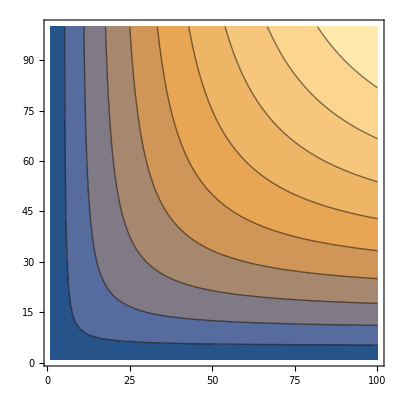

```mathematica
ContourPlot[i*j/(i+j),{i,1,100},{j,1,100}]
```

```mathematica
Solve[1/x+1/2==1/n,x,PositiveIntegers]
```

{{x→ConditionalExpression[2, n==1]}}

```mathematica
Integrate[-nx/(n-x),x]
```

nx Log[n-x]

```mathematica
x*Log[1-x]
```

x Log[1-x]

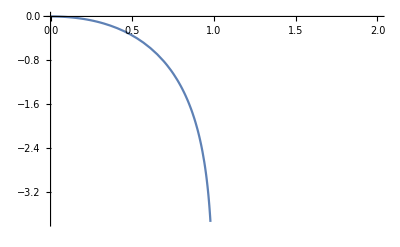

```mathematica
Plot[x Log[1-x]-x0*Log[1-0],{x,0,2}]
```